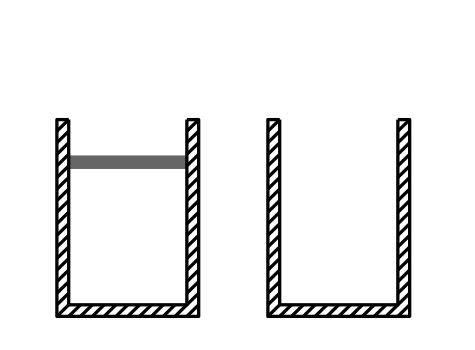

```mathematica
Module[{δ},
δ=0.07;
Graphics[{
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,0.9},{0.7,0.9-0.075}]},
{Thickness[0.005],
Line[{{0,1.12},{0,0},{0.7,0},{0.7,1.12}}],Line[{{1.25,1.12},{1.25,0},{1.95,0},{1.95,1.12}}],
(**)
Line[{{0,1.12},{-δ,1.12},{-δ,-δ},{0.7+δ,-δ},{0.7+δ,1.12},{0.7,1.12}}],
Table[Line[{{n*δ,0},{δ*(n-1),-δ}}],{n,0,11}],
Table[{
Line[{{-δ,n*δ},{0,δ*(n+1)}}],
Line[{{0.7,n*δ},{0.7+δ,δ*(n+1)}}]
},{n,0,15}],
(**)
Line[{{1.25,1.12},{1.25-δ,1.12},{1.25-δ,-δ},{1.95+δ,-δ},{1.95+δ,1.12},{1.95,1.12}}],
Table[Line[{{1.25+n*δ,0},{1.25+δ*(n-1),-δ}}],{n,0,11}],
Table[{
Line[{{1.25-δ,n*δ},{1.25,δ*(n+1)}}],
Line[{{1.95,n*δ},{1.95+δ,δ*(n+1)}}]
},{n,0,15}]
}
},ImageSize->{475,350},PlotRange->{{-0.15,2.15},{-δ-0.01,1.65}}]
]
```

```mathematica
Graphics[{
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,0.9},{0.7,0.9-0.075}]},
{Thickness[0.005],
Line[{{0,1.12},{0,0},{0.7,0},{0.7,1.12}}],Line[{{1.25,1.12},{1.25,0},{1.95,0},{1.95,1.12}}],
(**)
Line[{{0,1.12},{-0.07,1.12},{-0.07,-0.07},{0.77,-0.07},{0.77,1.12},{0.7,1.12}}],
Table[Line[{{n*0.07,0},{0.07*(n-1),-0.07}}],{n,0,11}],
Table[{Line[{{-0.07,n*0.07},{0,0.07*(n+1)}}],Line[{{0.7,n*0.07},{0.77,0.07*(n+1)}}]},{n,0,15}],
(**)
Line[{{1.25,1.12},{1.18,1.12},{1.18,-0.07},{2.02,-0.07},{2.02,1.12},{1.95,1.12}}],
Table[Line[{{1.25+n*0.07,0},{1.25+0.07*(n-1),-0.07}}],{n,0,11}],
Table[{Line[{{1.18,n*0.07},{1.25,0.07*(n+1)}}],Line[{{1.95,n*0.07},{2.02,0.07*(n+1)}}]},{n,0,15}]
}
},ImageSize->{475,350},PlotRange->{{-0.15,2.15},{-0.07-0.01,1.65}}]
```

-Graphics-

```mathematica
Manipulate[
Module[{choose1,P1,P2,go,Pint,Pext1,piston,height,δ1,L1,row1,row2,row3},
choose1[c1_,c2_,c3_,c4_]=Which[pick1==1,c1,pick1==2,c2,pick1==3,c3,pick1==4,c4];

P1=If[bn==1,0.1,2];
P2=If[bn==1,Pf1,Pf2];
go=If[bn==1,go1,go2];

Pint=(P1+(P2-P1)*go);
Pext1=If[pick1==1∨pick1==2,Pint,P2];

h1=0.1+0.8*((1-go)+If[bn==1,(P2-1)/(2-1)]*go);
h2=h1+0.075;
piston=0.9;height=0.055;
δ1=0.01501;L1=0.05325;

row1=Table[Rectangle[{n*δ1+(n-1)*L1,piston},{n*δ1+n*L1,piston+height}],{n,1,10}];
row2=Table[Rectangle[{n*δ1+(n-1)*L1,piston+height},{n*δ1+n*L1,piston+2*height}],{n,1,10}];
row3=Table[Rectangle[{n*δ1+(n-1)*L1,piston+2*height},{n*δ1+n*L1,piston+3*height}],{n,1,10}];

Graphics[{
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,h1},{0.7,h2}]},
{Thickness[0.005],Line[{{0,1.12},{0,0},{0.7,0},{0.7,1.12}}],Line[{{1.25,1.12},{1.25,0},{1.95,0},{1.95,1.12}}]},
{EdgeForm[Thick],If[bn==1,RGBColor[0.,0.19,0.52],RGBColor[0.,0.72,0.67]],row1,row2,row3},
(*Text[Column[{Length[row1],Length[row2],Length[row3]}],{0.35,0.5}],*)
Text[Style[choose1["reversible isothermal","reversible adiabatic","irreversible isothermal","irreversible adiabatic"],17],{0.35,1.5}],
(*Text[Style[Row[{"P_ext = ",Pext1}],17],{0.35,1.17*)
},ImageSize->{475,350},PlotRange->{{-0.15,2.15},{-0.1,1.65}}]
],
Control[{{bn,1,""},{1->"compression",2->"expansion"}}],
Style["choose two conditions:",Bold],
Row[{
Control[{{pick1,2,""},{1->"reversible isothermal",2->"reversible adiabatic",3->"irreversible isothermal",4->"irreversible adiabatic"},PopupMenu}],
Control[{{pick2,4,""},{1->"reversible isothermal",2->"reversible adiabatic",3->"irreversible isothermal",4->"irreversible adiabatic"},PopupMenu}]}],
PaneSelector[{
1->Column[{
Control[{{Pf1,1.5,"final pressure (MPa)"},1,2,0.1,Appearance->"Labeled"}],
Control[{{go1,0,""},0,1,Trigger,AnimationRate->0.25,AppearanceElements->{"PlayPauseButton","ResetButton"}}]}],
2->Column[{
Control[{{Pf2,0.6,"final pressure (MPa)"},0.1,1,0.1,Appearance->"Labeled"}],
Control[{{go2,0,""},0,1,Trigger,AnimationRate->0.5,AppearanceElements->{"PlayPauseButton","ResetButton"}}]}]
},Dynamic@bn]
]
```